```mathematica
NotConverged[ϕ_, ϕref_,ϵ_:.01]:=Max[Abs[ϕ-ϕref]]>ϵ

Gradients[ϕ_]:=Table[{ϕ[[i,j]]-ϕ[[i,j-1]],ϕ[[i,j]]-ϕ[[i-1,j]]},
{j,2,Dimensions[ϕ][[1]]},{i,2,Dimensions[ϕ][[2]] }]

PlotPotential[ϕ_]:=Show[{ListDensityPlot[-ϕ,ColorFunction->ColorData["RedBlueTones"]],
ListStreamPlot[Gradients[-ϕ]]}]
ϕJacobi[ϕ_, ρ_,a_:1,ϕ0_:0]:=a^2/4 ρ+1/4 Table[
If[
j==1||j==Ν||i==1||i==Ν,
ϕ0,
ϕ[[i+1,j]]+ϕ[[i-1,j]]+ϕ[[i,j+1]] + ϕ[[i,j-1]]
]
,{i,1,Ν}
,{j,1,Ν}
]

DoJacobi[ϕs_,ρ_,ϵ_]:=NestWhile[ϕJacobi[#,ρ]&,ϕs,(NotConverged[##,ϵ])&,2];

RectangleInMatrix[x1_,x2_,y1_,y2_,Ν_]:=Table[If[j<=x2&&j>=x1&&i<=y2&&i>=y1,1.0,0.0],{i,1,Ν},{j,1,Ν}];
```

```mathematica
Ν=100;
(* startwert *)
ϕs=Table[If[j==Ν||i==Ν||j==1||i==1,0.0,0.0],{i,1,Ν},{j,1,Ν}];
ρ1=-RectangleInMatrix[20,40,20,40,Ν]+RectangleInMatrix[60,80,60,80,Ν];
ρ2=-RectangleInMatrix[20,25,20,80,Ν]+RectangleInMatrix[75,80,20,80,Ν];
```

{86.75,Null}

{70.39,Null}

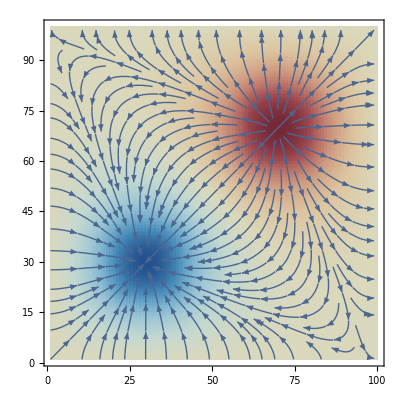

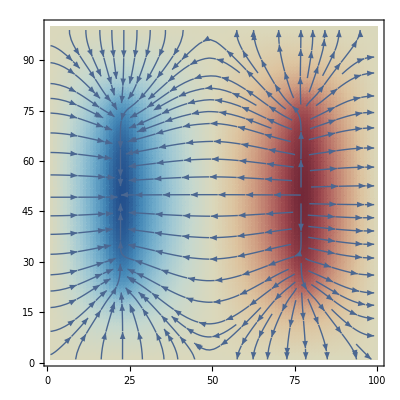

```mathematica
Timing[ϕ1=DoJacobi[ϕs,ρ1,0.01];]
Timing[ϕ2=DoJacobi[ϕs,ρ2,0.01];]
PlotPotential[ϕ1]
PlotPotential[ϕ2]
```

{19.6333,Null}

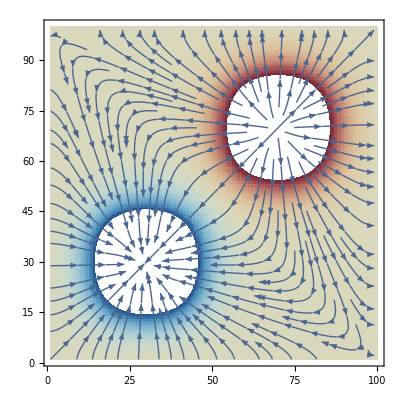

```mathematica
ϕGS[ϕ_,ρ_,w_:1]:=
Table[
If[
j==1||j==Ν||i==1||i==Ν,
0.,
(1-w)ϕ[[i,j]]+w/4. ρ[[i,j]]+(ϕ[[i+1,j]]+ϕ[[i-1,j]]+ϕ[[i,j+1]] + ϕ[[i,j-1]])/(4./w)
]
,{i,1,Ν}
,{j,1,Ν}
]


DoGS[ϕs_,ρ_,w_,ϵ_]:=NestWhile[ϕGS[#,ρ,w]&,ϕs,(NotConverged[##,ϵ])&,2];
Timing[ϕ3=DoGS[ϕs,ρ1,1,.1];]
PlotPotential[ϕ3]
```

```mathematica
times=Timing[ϕ3=DoGS[ϕs,ρ1,#,.1];]&/@Range[1.,2.,.3]
```

$Aborted